## Exercise 3

The objective of this task is to implement the Approximate Message Passing (AMP) algorithm for spiked matrix estimation based on the problems discussed in Exercise 2. The goal is to explore and analyze the performance of the AMP algorithm across the signal distributions already considered and compare its performance with the prediction of optimal estimators derived theoretically.

The AMP can be derived with the cavity method and it is characterized by  iterative updates for estimating the signal . The algorithm is completely specified by the prior  of the signal distribution and relies on a denoising function, that is adapted to this prior:
											

The corresponding updates for AMP are as follows (derivation in pdf file):
• Gaussian Prior:
												
• Rademacher Prior:
											
• Rademacher-Bernoulli Prior:
									

AMP is based on iterative update accordingly with the 	following scheme:
									 		
													
NOTE: albeit we have vector variable, since by assumption they are i.i.d and  does not mix the components, the updates act component by component.

```mathematica
n=1000; (*number of variables*)
 
(*Rademacher*)
eta[A_,B_]:=N[Tanh[B]]; (* denoising function*)
etaPrime[A_,B_]:=N[1-Tanh[B]^2]; (*Derivative of eta[Vector]*)


(*Gaussian*)
eta1[A_,B_]:=N[B/(1+A)]; (* denoising function*)
etaPrime1[A_,B_]:=N[1/(1+A)*ConstantArray[1,Length[B]]]; (*Derivative of eta[vector]*)

(*Rademacher-Bernoulli*)
rho =1;
eta2[A_,B_]:=N[rho*Tanh[B]/(rho + Exp[A/2]*(1-rho)/Cosh[B])]; (* denoising function*)
etaPrime2[A_,B_]:= N[rho*( Exp[A/2]*(1-rho)*Cosh[B]+rho)/( Exp[A/2]*(1-rho)+Cosh[B]*rho)^2]; (*Derivative of eta*)



Damper[xOld_,xNew_, Damping_] := xOld*Damping + (1-Damping)*xNew;


IterateAMP[Tol_,MaxIter_,Damping_,n_,Y_,Init_,SNR_]:=Module[{
xHatOld=ConstantArray[0,n],
xHat=Init,
aOld=0,(*Scalar*)
bOld=ConstantArray[0,n],(*vector*)
sigma=0,
Convergence=False,
a,b (*new auxiliary variables*)},
For[t=0,t<MaxIter,t++,
sigma=Total[etaPrime[aOld,bOld]];(*Compute a and b using the updated formulas with damping*)
a=Damper[aOld,SNR*xHat.xHat/n,Damping](*Damp scalar a*);
b=Damper[bOld,Sqrt[SNR/n]*Transpose[Y].xHat-SNR/n*sigma*xHatOld,Damping](*Damp vector b*);
xHatOld=xHat;(*Update xHat*)
xHat=eta[a,b];(*Apply denoising function*)
(*Update the old variables*)
aOld=a;
bOld=b;
(*Compute the distance for convergence*)
distance=Min[(xHat-xHatOld).(xHat-xHatOld),(xHat+xHatOld).(xHat+xHatOld)];
If[distance<Tol,(Convergence=True;Break[]),]];
Return[{xHat,Convergence,t}]];



(*Parameters for iterations*)
maxIter=10^5; (*Maximum number of iterations*)
tolerance=10^-7; (*Convergence criterion*)
Damping = 0.3;
```

{0.1,True,0.985216,11}

{0.2,True,0.985218,12}

{0.3,True,0.985218,14}

{0.4,True,0.985217,17}

{0.5,True,0.985217,21}

{0.6,True,0.985215,25}

{0.7,True,0.985215,30}

{0.8,True,0.985212,36}

{0.9,True,0.985214,44}

{1.,True,0.985204,56}

{1.1,True,0.985208,76}

{1.2,True,0.9852,109}

{1.3,True,0.985195,194}

{1.4,True,0.985179,820}

{1.5,False,0.996558,100000}

{1.6,False,1.02428,100000}

{1.7,False,1.00333,100000}

{1.8,False,1.05382,100000}

{1.9,False,1.04509,100000}

{2.,False,1.06647,100000}

{2.1,False,1.09253,100000}

{2.2,False,1.06547,100000}

{2.3,False,1.10306,100000}

{2.4,False,1.08649,100000}

{2.5,True,0.839124,72154}

{2.6,False,1.10932,100000}

{2.7,False,0.665257,100000}

{2.8,False,0.742388,100000}

{2.9,False,0.402316,100000}

{3.,True,0.325086,191}

{3.1,True,0.271694,54}

{3.2,True,0.227569,27}

{3.3,True,0.238271,34}

{3.4,True,0.202759,24}

{3.5,True,0.178359,23}

{3.6,True,0.210789,27}

{3.7,True,0.194266,21}

{3.8,True,0.161098,17}

{3.9,True,0.1709,18}

{4.,True,0.1731,18}

{4.1,True,0.150153,16}

{4.2,True,0.149109,16}

{4.3,True,0.13522,14}

{4.4,True,0.144553,15}

{4.5,True,0.128574,14}

{4.6,True,0.1405,14}

{4.7,True,0.123247,13}

{4.8,True,0.12769,13}

{4.9,True,0.12384,13}

{5.,True,0.119503,13}

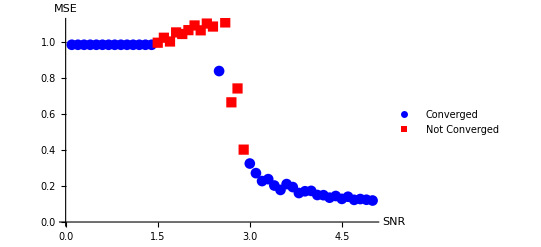

```mathematica
(*Gaussian prior*)
results={};
resultsNOCONV = {};
 (*True values*)
xGauss = Table[Sqrt[2]*InverseErf[2*Random[]-1],{i,1,n}];

For[SNR=0.1,SNR<=5,SNR=SNR+0.1,
noise = Table[Sqrt[2]*InverseErf[2*Random[] - 1],{i, 1, n},{j,1,n}];
noise = (noise+Transpose[noise])/2;
yGauss=Outer[Times,xGauss,xGauss]*Sqrt[SNR/n]+ noise;(*Noisy observation*)
Init = 10^-3*Table[Sqrt[2]*InverseErf[2*Random[]-1],{i,1,n}]+xGauss; (*Informed initializtion*)
(*Random init xGauss = Table[Sqrt[2]*InverseErf[2*Random[]-1],{i,1,n}];*)
{xHat,Convergence,t}=IterateAMP[tolerance,maxIter,Damping,n,yGauss,Init,SNR];
MSE = Min[(xGauss-xHat) . (xGauss-xHat),(xGauss+xHat) . (xGauss+xHat)]/n;

If[Convergence,AppendTo[results,{SNR,MSE}],AppendTo[resultsNOCONV,{SNR,MSE}]];

Print[{SNR,Convergence,MSE,t}];
]

(*Plot SNR vs.MSE*)
ListPlot[{results,resultsNOCONV  },PlotStyle->{Blue,Red},PlotLegends->{"Converged","Not Converged"},AxesLabel->{"SNR","MSE"},PlotMarkers->Automatic,Joined->False]
```

{0.1,True,0.999996,11}

{0.3,True,0.999998,14}

{0.5,True,0.999996,21}

{0.7,True,0.999993,30}

{0.9,True,0.999986,45}

{1.1,True,0.999983,78}

{1.3,True,0.999964,199}

{1.5,False}

{1.5,False,0.74301,100000}

{1.7,False}

{1.7,False,0.494349,100000}

{1.9,False}

{1.9,False,0.470466,100000}

{2.1,False}

{2.1,False,0.283762,100000}

{2.3,False}

{2.3,False,0.170619,100000}

{2.5,True,0.060355,17}

{2.7,True,0.0402962,16}

{2.9,True,0.036868,14}

{3.1,True,0.0270654,13}

{3.3,True,0.0168098,12}

{3.5,True,0.0272074,11}

{3.7,True,0.0128253,11}

{3.9,True,0.0049194,10}

{4.1,True,0.0079085,10}

{4.3,True,0.00348604,10}

{4.5,True,0.00997689,9}

{4.7,True,0.0121369,8}

{4.9,True,0.00483343,10}

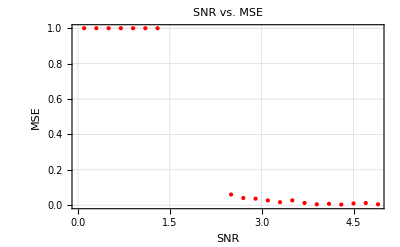

```mathematica
(*Rademacher Prior*)
(*NB need to change eta and eta prime in the function*)
results={};
xRad = Table[Sign[Random[] - 0.5],{i,1,n}]; (*True values*)

For[SNR=0.1,SNR<=5,SNR=SNR+0.2,
noise = Table[Sqrt[2]*InverseErf[2*Random[] - 1],{i, 1, n},{j,1,n}];
noise = (noise+Transpose[noise])/2;
yRad=Outer[Times,xRad,xRad]*Sqrt[SNR/n]+ noise;(*Noisy observation*)
Init = 10^-3*Table[Sqrt[2]*InverseErf[2*Random[]-1],{i,1,n}]+xRad; (*Informed init*)
(*Random INIT xRad = Table[Sign[Random[] - 0.5],{i,1,n}];*)
{xHat,Convergence,t}=IterateAMP[tolerance,maxIter,Damping,n,yRad,Init,SNR];
MSE = Min[(xRad-xHat) . (xRad-xHat),(xRad+xHat) . (xRad+xHat)]/n;

If[Convergence,AppendTo[results,{SNR,MSE,t}],Print[{SNR, Convergence}]];

Print[{SNR,Convergence,MSE,t}];
]

snrValues=results[[All,1]];
mseValues=results[[All,2]];

(*Plot SNR vs.MSE*)
ListPlot[Transpose[{snrValues,mseValues}],PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"SNR","MSE"},PlotLabel->"SNR vs. MSE",GridLines->Automatic,Frame->True]
```